Метод на допирателните

Условия за намиране на корен на уравнението f (x) = 0  с точност ε:
1. f ∈ C^2[a,b]
2. f(a).f(b) < 0
3. f'(x), f''(x) имат постоянен знак в [a,b].
Тогава итерационният процес:

x_(n+1)=x_n- (f(x_n))/(f'(x_n)),

n = 0,1,2,...e сходящ към единствения корен x^*на f (x)=0.
x_0 - такова, че f(x_0)f''(x)>0;

За оценка на грешката имаме :
|x^*-x_n|⩽ M_2/(2 m_1)|x_n-x_(n-1)|^2

където M_2= max_[a,b] |f''(x)|, m_1= min_[a,b] |f'(x)|.

Задача 1. По метода на допирателните да се намери коренът на уравнението
 sin(x)-x+0,15=0 с точност ε = 10^-4.

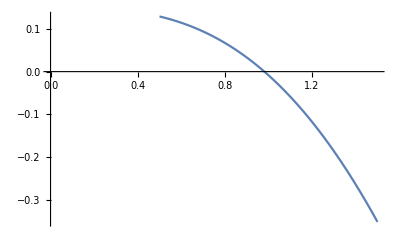

```mathematica
Clear[f,x,a,b]
f[x_]:=Sin[x]-x+0.15
Plot[f[x],{x,0.5,1.5},AxesOrigin->{0,0}]
```

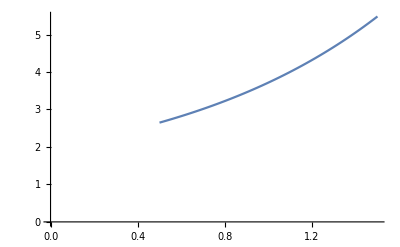

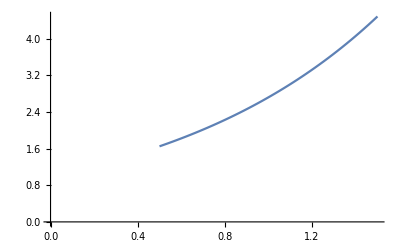

```mathematica
Clear[a,b,x0,x];
a=0.5;b=1.5;
Plot[f'[x],{x,a,b},AxesOrigin->{0,0}]
Plot[f''[x],{x,a,b},AxesOrigin->{0,0}]
```

```mathematica
x0=1.5;Print["Начално приближение: x0 = ",x0]
err=∞;eps=10^-4;
n=0;
Print["   n = ",n,"   x = ",x0,"   f[x]=",f[x0],"   err=",err];
While[err>eps,
n=n+1;
x1=x0-f[x0]/f'[x0];
err=Abs[(x1-x0)];
x0=x1;
Print["   n = ",n,"   x = ",x0,"   f[x]=",f[x0],"   err=",err];
];
Print["Отговор x^*~ ",x0, " с грешка ", err]
```

Начално приближение: x0 = 1.5

n = 0   x = 1.5   f[x]=5.98169   err=∞

n = 1   x = 0.408787   f[x]=1.91378   err=1.09121

n = 2   x = -0.355199   f[x]=0.345835   err=0.763986

n = 3   x = -0.558508   f[x]=0.0135545   err=0.203309

n = 4   x = -0.56713   f[x]=0.0000212028   err=0.00862211

n = 5   x = -0.567143   f[x]=5.19078×10^-11   err=0.0000135295

Отговор x^*~ -0.567143 с грешка 0.0000135295

```mathematica
Solve[f[x]==0]
```

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

Solve[0.15-x+Sin[x]==0]

```mathematica
FindRoot[f[x],{x,1}]
```

{x→-0.567143}

Задача 2 
По метода на допирателните да се намери с точност 10^-4 най-големият отрицателен коренът на уравнението tg x-x+0.25=0.

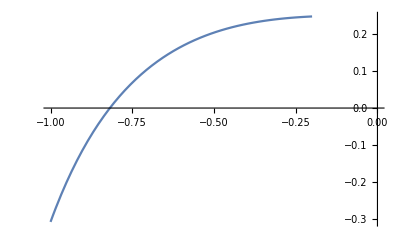

```mathematica
Clear[f,x,a,b]
f[x_]:=Tan[x]-x+0.25
Plot[f[x],{x,-1,-0.2},AxesOrigin->{0,0}]
```

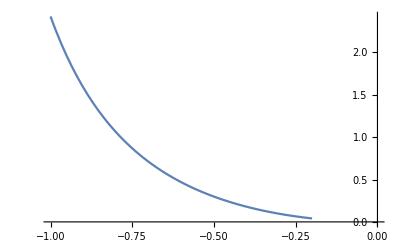

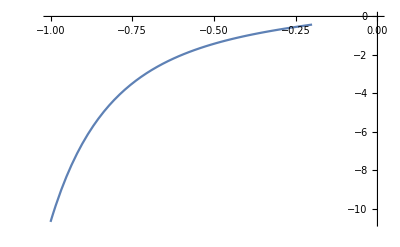

```mathematica
Clear[a,b,x0,x];
a=-1.;b=-0.2;
Plot[f'[x],{x,a,b},AxesOrigin->{0,0}]
Plot[f''[x],{x,a,b},AxesOrigin->{0,0}]
```

```mathematica
x0=-1.;Print["Начално приближение: x0 = ",x0]
err=∞;eps=10^-4;
n=0;
Print["   n = ",n,"   x = ",x0,"   f[x]=",f[x0],"   err=",err];
While[err>eps,
n=n+1;
x1=x0-f[x0]/f'[x0];
err=Abs[(x1-x0)];
x0=x1;
Print["   n = ",n,"   x = ",x0,"   f[x]=",f[x0],"   err=",err];
];
Print["Отговор x^*~ ",x0, " с грешка ", err]
```

Начално приближение: x0 = -1.

n = 0   x = -1.   f[x]=-0.307408   err=∞

n = 1   x = -0.873261   f[x]=-0.0699371   err=0.126739

n = 2   x = -0.824138   f[x]=-0.00650655   err=0.0491227

n = 3   x = -0.818567   f[x]=-0.000072164   err=0.00557166

n = 4   x = -0.818503   f[x]=-9.13962×10^-9   err=0.0000631915

Отговор x^*~ -0.818503 с грешка 0.0000631915

```mathematica
x=.
FindRoot[f[x],{x,-1}]
```

{x→-0.818503}

Задача 3.
Да се намери с точност  10^-6 коренът на уравнението ⅇ^x-x^2-x-1=0.